# Mentor Talk: WL Document Processing

## for Wolfram Summer Program 2024/Jack Heseltine (Mentor)

## Basic PDF Functionality

Let’s say you have a plot:

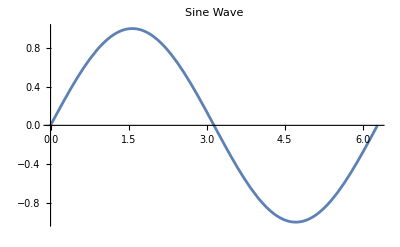

```mathematica
Plot[Sin[x],{x,0,2*Pi},PlotLabel->"Sine Wave"]
```

How would you export this, say, to use in another context?

Answer:

```mathematica
plot=Plot[Sin[x],{x,0,2*Pi},PlotLabel->"Sine Wave"];
Export["sine_wave.pdf",plot]
```

Ok, where did that get exported to? Evaluate the following to find that directory:

```mathematica
Directory[]
```

```mathematica
(*Change the directory to a specific path if needed*)
SetDirectory["/desired/path/to/save"]
```

## Custom Recursion-Based Function

Have you used Module like this before? If no, take a quick read into the documentation. (Half of software development is reading the docs.) This is based on the convertToLatexDox/convertToLatexAndPdfDocs from the presentation but does without LATEX, the typesetting language frequently used in other academic contexts.

```mathematica
convertToLatexDoc[notebookPath_]:=Module[{nb,content,latexPath,latexTemplatePath,resourceDir=$resDir,texResult,sownData,filledContent},If[Length[$tmaData]==0,(*Issue message if Theorema-Formula-Data not provisioned*)Message[tmaDataImport::empty,"The Theorema-Formula-Datastructure is empty. 
		Did you evaluate a Theorema notebook before loading the package and calling the conversion function?"];
(*Additional handling for empty data can be added here*)Return[$Failed]];
nb=NotebookOpen[notebookPath,Visible->False];
content=NotebookGet[nb];
NotebookEvaluate[content];(*on content:important,so that Tma env.variables are available in any case*)latexPath=getLatexPath[notebookPath];
latexTemplatePath=getLatexTemplatePath[notebookPath];
(*filledContent=fillLatexTemplate[resourceDir,<|"nbName"->FileBaseName[notebookPath]|>];*){texResult,sownData}=Reap[parseNbContent[content],{"title","author","date"}];
filledContent=fillLatexTemplate[resourceDir,<|"nbContent"->texResult,"nbTitle"->First[sownData[[1,1]]],"nbAuthor"->First[sownData[[2,1]]],"nbDate"->First[sownData[[3,1]]]|>];
Export[latexPath,filledContent,"Text"];
(*Print[Theorema`Common`$tmaEnv];*)]

convertToLatexAndPdfDocs[notebookPath_]:=Module[{latexPath,pdfPath,compileCmd,conversionResult},conversionResult=convertToLatexDoc[notebookPath];
If[conversionResult===$Failed,Return[$Failed]];
(*Compile LaTeX to PDF using pdflatex*)latexPath=getLatexPath[notebookPath];
pdfPath=StringReplace[latexPath,".tex"->".pdf"];
compileCmd="pdflatex -interaction=nonstopmode -output-directory="<>DirectoryName[latexPath]<>" "<>latexPath;
RunProcess[{"cmd","/c",compileCmd}];]
```

## Offloading to a .wl-File/Calling from another Notebook and the Command Line (a.k.a. Challenges)

### Design

Come up with a pipeline-like (export-PDF) scenario that you could use WL for! A pipeline could be Get Current Weather Data -> Present in some Plot -> Export the Plot to a shared Weather Report Directory.

Now take it one step further! Maybe you want this task to regularly occur: Do you have an idea for how one might do such a thing? (I.e. automate weather-plot generation to a directory, say, always on the hour.)

Think about it for a moment then move on the main challenge, Offloading to .wl-File: this is the basis for a couple of cool things we can then go on to do to solve some problems and/or automate some tasks.

### Offloading to .wl-File

Make .wl file, move your function (e.g. the (adapted) Custom Recursion-Based Function from above) there, save the file, e.g. to a new scripts directory.

#### Calling from another Notebook

Start another notebook and simply do:

```mathematica
(* nb *)
(*Get["file.wl"]*)
(* or *)
<< "C:\\Users\\jackh\\OneDrive\\Documents\\WSRP2024\\mentor-talk\\file.wl"
```

You should now be able to load a (test) function defined in that file.

```mathematica
square[2] (* defined in file.wl, in the same directory as this nb *)
```

4

Notice the change of the font color of the function name once you type it out in full if it is found somewhere in the scope.

For the challenge, try calling your own .wl-file function from another notebook. You might like to work in an IDE (Integrated Development Environment) like Visual Studio Code.

#### Calling from a Command Line

Open a command prompt (Windows) or terminal (Mac) and type “wolframscript” and hit Enter to see if it is installed. You should be able to feed a WL-Kernel input like this:

To run a .wl-file: wolframscript -file /path/to/example.wl
To run with arguments: wolframscript -file path/to/your/file.wl -code “Print[yourFunctionName[arguments]]”

For example, assuming a .wl file with the contents -

```mathematica
(* file.wl *)
square[x_] := x^2

cube[x_] := x^3
```

- we would get:

```mathematica
(* command line *)
wolframscript -file /path/to/file.wl -code "Print[square[3]]"
(* Output: 9 *)

wolframscript -file /path/to/file.wl -code "Print[cube[2]]"
(* Output: 8 *)
```

For the challenge, try calling your own .wl-file function from the command line.

### + Putting on a Timer (Optional)

Windows:

Use the Task Scheduler (Press Win + R, type taskschd.msc, and press Enter) to configure a “Basic Task.”

See these screenshots -
-Graphics-
-Graphics-

Actually slightly easier on Mac:

Go to crontab editor

```mathematica
crontab -e (* terminal *)
```

crontab-e

Add “cronjob”

```mathematica
0 * * * * wolframscript -file /path/to/your/file.wl -code "Print[square[3]]" >> /path/to/output.log 2>&1 (* croneditor *)
```

Try putting your script on a timer!

### ++ Deploying to the Cloud (Optional Extra Credit)

Check your Cloud Parameters

```mathematica
$CloudConnected
```

True

If not connected (you can explicitly add the Cloud User ID you want to connect with):

```mathematica
CloudConnect["heseltine@wolfram.com"]
```

heseltine@wolfram.com

Then to check:

```mathematica
$CloudUserID
```

heseltine@wolfram.com

Finally:

```mathematica
(*Define the function*)square[x_]:=x^2

(*Define the task*)
task:=Module[{result},result=square[3];
CloudExport[result,"Text",CloudObject["/output/square3.txt"]]];

(*Deploy the scheduled task to run every hour*)
CloudDeploy[ScheduledTask[task[],Quantity[1,"Hours"]],"HourlySquareTask"]
```

CloudObject[https://www.wolframcloud.com/obj/heseltine/HourlySquareTask]

Check the URL:

Another fun idea: Process your email! 

Anyway, Final Challenge: Deploy your function to the Cloud.

You can both pause -

- and delete Scheduled Tasks.